Pumping power is -10.11dBm.

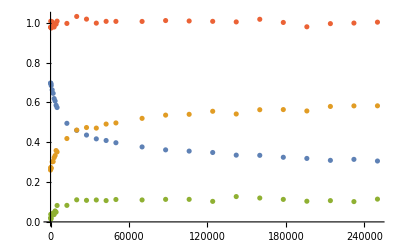

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"optimal_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 5.dBm.

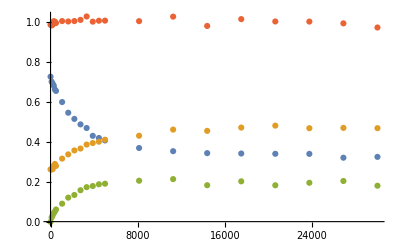

```mathematica
file=path<>"high_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is -25.dBm.

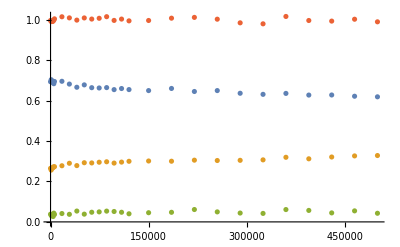

```mathematica
file=path<>"low_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

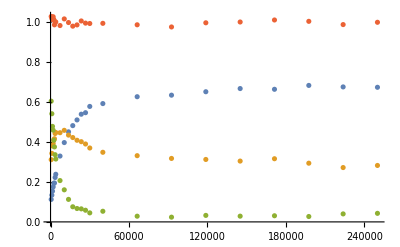

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

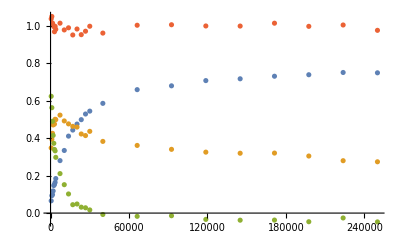

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay_0122.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

{1200.,2960.,4720.,6480.,8240.,10000.,16000.,22000.,28000.,34000.,40000.,82000.,124000.,166000.,208000.,250000.}

Pumping power is 25.dBm.

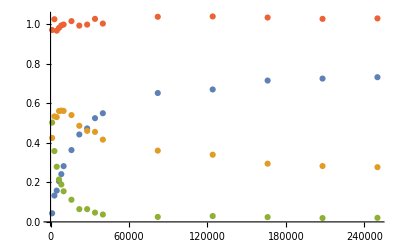

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay_interleaved.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
Time = data["/time"]
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{Time,P0}];
P1toPlot=Transpose[{Time,P1}];
P2toPlot=Transpose[{Time,P2}];
PSumtoPlot=Transpose[{Time,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

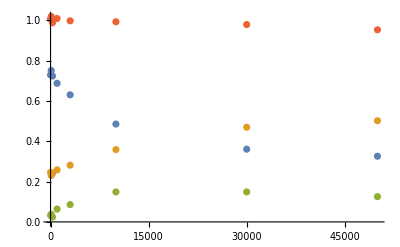

```mathematica
file=path<>"transient_P2_P1_interleaved.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

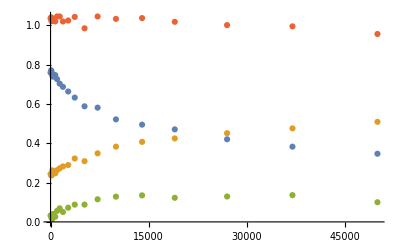

```mathematica
file=path<>"transient_P2_P1_interleaved_more_points.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

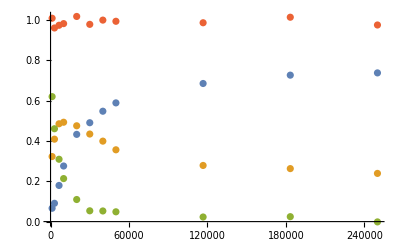

```mathematica
file=path<>"t1_population_2020-02-10-04-07-55.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 20.dBm.

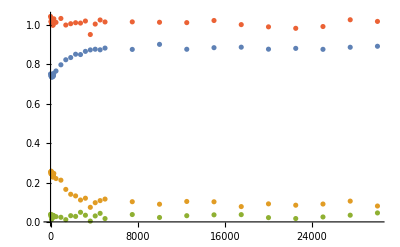

```mathematica
file=path<>"transient_1_3_pumping.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

```mathematica
Transpose@{Time,P0}
```

{{0.,0.75193},{0.03,0.742714},{0.06,0.73968},{0.09,0.737979},{0.12,0.735022},{0.15,0.741783},{0.18,0.744428},{0.21,0.738526},{0.24,0.740155},{0.27,0.7451},{0.3,0.755156},{0.5,0.767037},{0.95,0.798438},{1.4,0.824075},{1.85,0.835303},{2.3,0.852225},{2.75,0.850462},{3.2,0.866686},{3.65,0.874151},{4.1,0.877612},{4.55,0.874623},{5.,0.883382},{7.5,0.876637},{10.,0.902292},{12.5,0.877377},{15.,0.885431},{17.5,0.887997},{20.,0.877848},{22.5,0.881929},{25.,0.877068},{27.5,0.887604},{30.,0.892653}}

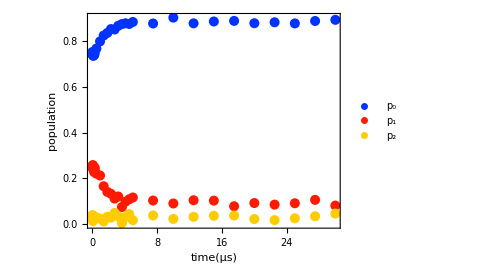

```mathematica
PtSize=0.02;
Time=PumpingTime/1000;
g=Show[ListPlot[{Transpose@{Time,P0},Transpose@{Time,P1},Transpose@{Time,P2}}, PlotStyle->{{PointSize[PtSize],RGBColor[0,0.2,1]},{PointSize[PtSize],RGBColor[1,0.1,0]},{PointSize[PtSize],RGBColor[1,0.8,0]}},PlotLegends->Placed[PointLegend[{"p_0","p_1","p_2"},LegendFunction->(Framed[#]&),LabelStyle->{FontFamily->"Times New Roman",Black,14}],{Right,Center}]]
,Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75,FrameLabel->{Style["time(μs)",Black,18,FontFamily->"Times New Roman"],Style["population",Black,18,FontFamily->"Times New Roman"]}]
```

```mathematica
Export[path<>"13pumping.pdf",g]
```

C:\SC Lab\GitHubRepositories\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\13pumping.pdf